## 3.029 Spring 2022 Lecture 21 - 04/20/2022

## Kinetic Monte Carlo

We have already seen Monte Carlo methods in L09-10

In general, they’re defined as computational algorithms which rely on repeated random sampling to solve deterministic problems

The canonical example of a Monte Carlo method is approximating π by counting points that fall inside/outside a circle

π≃  3.13296

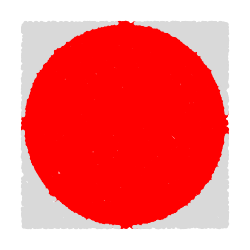

```mathematica
Block[{
rec=Rectangle[{-1,-1},{1,1}],
disk=Disk[],
pts,groupedByRegion,rm},
pts=RandomPoint[rec,25000];
rm=RegionMember[disk];
groupedByRegion=GroupBy[pts,rm];
Echo[4Length[groupedByRegion[True]]/25000.,"π≃"];
Graphics[MapThread[{#1,Point[#2]}&,{{Red,LightGray},Values@groupedByRegion}],ImageSize->250]
]
```

## Metropolis-Hastings Algorithm

In this lecture, we will look at a particular class of MC methods applicable to thermally-activated process

This is referred to as Kinetic Monte Carlo (KMC) in the Materials Science vernacular

It also goes by other popular names, such as Markov chain Monte Carlo (MCMC)

The are many flavours of KMC, but we will focus on the most popular “rejection-KMC” algorithm, given by the Metropolis-Hastings algorithm

In-fact, you saw this last semester in 3.019

We will briefly review the method in 1D, and then address one of its shortcomings

Consider a 1D potential energy surface, with a single particle

Suppose the particle makes an attempt to randomly move to the left or the right

If the energy of the final position is lower

the attempt is accepted with  probability, p = 1

If the energy of the final position  is higher

the attempt is accepted with probability,

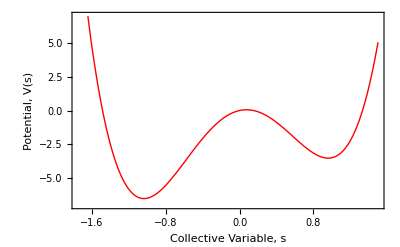

```mathematica
asymmetricDoubleWellPotential[s_]=5 s^4-10 s^2+3s/2;

basePlot=Plot[asymmetricDoubleWellPotential[s],{s,-7/4,3/2},Frame->True,PlotRange->{-7,7},PlotStyle->Directive[Red,Thick],ImageSize->400,LabelStyle->Directive[16,Black],FrameLabel->{"Collective Variable, s","Potential, V(s)"}]
```

Note: You’ll notice we called the x-axis a collective variable, s

This is because for higher-dimensional phase-spaces

e.g. an ammonia molecule, NH_3, has 12-degrees of freedom in 3D

but can be represented using 2 collective variables:
1. the radius, R, of the sphere constructed with the N-atom in the center and the H-atoms of the circumference
2. the height, Z,  of the N-atom above the plane of H-atoms

```mathematica
MoleculePlot3D["Ammonia",ImageSize->250,ViewPoint->{-5,10,-5}]
```

-Graphics3D-

It’s straight-forward to implement a single MCMC step

```mathematica
metropolisStep1D[energyFunction_, temperature_:0.5, stepsize_:0.05][position_]:= 
Module[{
attemptPosition = position + stepsize RandomChoice[{-1,1}],
energyBefore = energyFunction[position],deltaEnergy,probability
},
deltaEnergy = energyFunction[attemptPosition]- energyBefore;

If[deltaEnergy<= 0, Return[attemptPosition]];

probability = Exp[-deltaEnergy/temperature];
RandomChoice[{probability,1-probability}->{attemptPosition,position}]
]
```

We can investigate the results of 1000 MC simulations starting from a random initial position

```mathematica
SeedRandom[11];
startingPosition=RandomReal[{-7/4,3/2}]
unbiasedSimulation=NestList[metropolisStep1D[asymmetricDoubleWellPotential],startingPosition,1000];
```

-1.04234

Let’s animate this

```mathematica
Clear[monteCarloTrajectory]
monteCarloTrajectory[position_,energyFunction_:asymmetricDoubleWellPotential]:=Show[basePlot,Epilog->{PointSize[0.025],Point[{position,energyFunction[position]}]}]
```

```mathematica
Manipulate[
monteCarloTrajectory[unbiasedSimulation[[t]]],
{{t,1,"Monte Carlo State"},1,Length[unbiasedSimulation],1},Paneled->False]
```

Since we started near a local minimum, and our simulation’s temperature is low-enough

we're only sampling a small area of the potential energy surface

Important Note: The above slider gives the impression of “time”. However, the moves are chosen at random and have no physical meaning. They should instead be interpreted as plausible equilibrium states the system can access in that configuration at the specified temperature

This has important implications. Namely since we have no temporal information, we can only describe equilibrium properties and not dynamical properties

That’s it folks!

Despite its simplicity, the MCMC method is very useful in modeling many thermally-activated phenomena, such as:

Sintering

Surface Roughening

Vacancy Diffusion

Coarsening

Dislocation Mobility

etc..

## Meta-Dynamics

As we saw in our KMC simulation above, the MCMC simulation is likely to get “stuck” in a local energy minimum

There are many possible remedies for this, the simplest being increasing the temperature, however most are computationally expensive

This is because the particle spends most of its time in these local minima and very rarely (even at high temperatures) explores metastable configurations

Exploring these metastable states can be important when we wish to “reconstruct” an unknown potential energy surface

E.g. in the Ammonia molecule example above, we could simulate its trajectory using molecular dynamics, and from that information wish to recover the energy landscape

Metadynamics attempts to solve this by “filling” in the free energy minima using a history-dependent biasing potential

### Kernel Estimation

First, let’s investigate the locations visited by our unbiased MCMC simulation above

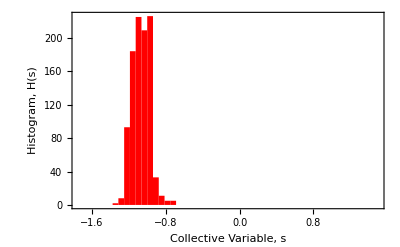

```mathematica
Histogram[unbiasedSimulation,{-7/4,3/2,1/16},Frame->True,ChartStyle->Directive[EdgeForm[None], Red],ImageSize->400,LabelStyle->Directive[16,Black],FrameLabel->{"Collective Variable, s","Histogram, H(s)"}]
```

as expected, the probability density is localized around the local minimum

Since we want our simulation to be differentiable, we instead want a “smooth” version of the histogram above

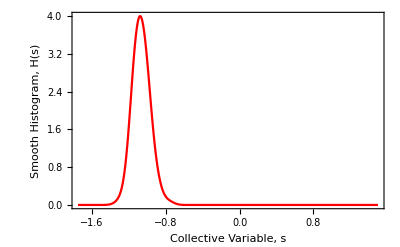

```mathematica
SmoothHistogram[unbiasedSimulation,{0.05,"Gaussian"},PlotRange->{{-7/4,3/2},All},Frame->True,PlotStyle->Red,ImageSize->400,LabelStyle->Directive[16,Black],FrameLabel->{"Collective Variable, s","Smooth Histogram, H(s)"}]
```

What the function above does is called kernel-estimation

where one uses a localized “kernel” to sample the data points and slowly build-up a probability density function given by

here,  is the bandwidth parameter, and  is the smoothing kernel

```mathematica
kernelDensityEstimation[kernel_,bandwidth_][data_][s_]:=With[{n=Length[data],h=bandwidth},
1/(n h)Sum[kernel[(s-data[[i]])/h],{i,n}]]
```

There are many possible smoothing kernels

```mathematica
Block[{kernels={"Biweight","Cosine","Epanechnikov","Gaussian","Rectangular","SemiCircle","Triangular","Custom"},dists},
dists=Table[SmoothKernelDistribution[{0},1,i],{i,(kernels/.{"Custom"->(PDF[CauchyDistribution[0,1],#]&)})}];
Multicolumn[Table[Plot[Evaluate[PDF[dists⟦i⟧,x]],{x,-3,3},PlotRange->All,ImageSize->100,PlotLabel->kernels⟦i⟧,Filling->Axis,Ticks->None],{i,Length[kernels]}],4,Appearance->"Horizontal"]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

We can indeed reproduce the SmoothHistogram output above using our own kernel density estimation implementation

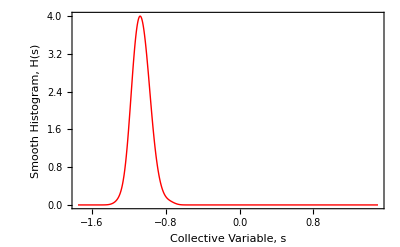

```mathematica
Block[{f,kernel=1/(√(2π))Exp[-#^2/2]&,bw=0.05},
f[s_]=kernelDensityEstimation[kernel,bw][unbiasedSimulation][s];
Plot[f[s],{s,-7/4,3/2},Frame->True,PlotRange->All,PlotStyle->Directive[Red,Thick],ImageSize->400,LabelStyle->Directive[16,Black],FrameLabel->{"Collective Variable, s","Smooth Histogram, H(s)"}]
]
```

Unsurprisingly, Mathematica has an built-in kernel density estimator, called SmoothKernelDistribution

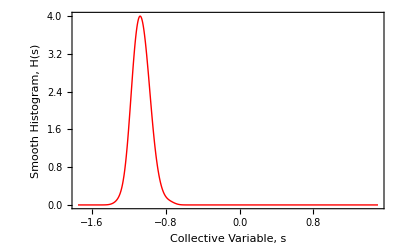

```mathematica
With[{f=PDF[SmoothKernelDistribution[unbiasedSimulation,0.05,"Gaussian"]]},
Plot[f[s],{s,-7/4,3/2},Frame->True,PlotRange->All,PlotStyle->Directive[Red,Thick],ImageSize->400,LabelStyle->Directive[16,Black],FrameLabel->{"Collective Variable, s","Smooth Histogram, H(s)"}]
]
```

### Potential Biasing

The idea is again simple:

We’ll run a MCMC simulation for a fixed number of iterations

Compute the kernel density probability

Bias the potential using our estimation

effectively “discouraging” already-visited locations

Rinse and repeat

```mathematica
biasPotential[biasedPotential_,positions_,w_:0.01,bw_:0.05]:=Block[{bs},
bs=PDF[SmoothKernelDistribution[positions,bw,"Gaussian"]];
biasedPotential[s]+w bs[s]
]
```

E.g. our biased potential after one iteration would look something like this

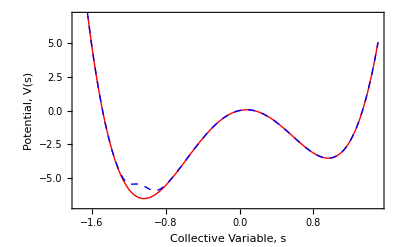

```mathematica
With[{f=biasPotential[asymmetricDoubleWellPotential,unbiasedSimulation,0.25]},
Show[basePlot,
Plot[f,{s,-7/4,3/2},PlotStyle->Directive[Blue,Dashed,Thick]]]
]
```

### Potential Energy Surface Reconstruction

Let’s wrap all of this in a function

We’ll use interpolating functions to avoid keeping track of all the exponentials explicitly

```mathematica
biasPotentialIfn[biasedPotential_InterpolatingFunction,positions_,w_:0.01,bw_:0.05,interpolationPts_:500]:=Block[{bs,pts},
pts=Subdivide[-7/4.,3/2,interpolationPts];
bs=PDF[SmoothKernelDistribution[positions,bw,"Gaussian"],pts];
Interpolation[Thread[{pts,w bs+biasedPotential[pts]}],InterpolationOrder->1]
]
```

```mathematica
Clear[simulateFixedNumberOfSteps]
simulateFixedNumberOfSteps[biasedPotential_,positions_,steps_:250,temperature_:0.5,stepsize_:0.05]:=Module[
{position0=Last[positions],force},
Rest[NestList[metropolisStep1D[biasedPotential,temperature,stepsize],position0,steps]]
]
```

```mathematica
Clear[updateBiasedPotential]
updateBiasedPotential[steps_:250,temperature_:0.5,stepsize_:0.05,w_:0.05,bw_:0.05,interpolationPts_:500][{biasedPotential_InterpolatingFunction,positions_}]:=Block[{newPositions,newPotential},
newPositions=simulateFixedNumberOfSteps[biasedPotential,positions,steps,temperature,stepsize];
newPotential=biasPotentialIfn[biasedPotential,newPositions,w,bw,interpolationPts];
{newPotential,newPositions}
]
```

Starting with our unbiased potential

```mathematica
asymmetricDoubleWellPotentialIfn=With[{pts=Subdivide[-7/4.,3/2,500]},Interpolation[Thread[{pts,asymmetricDoubleWellPotential[pts]}],InterpolationOrder->1]]
```

InterpolatingFunction[…]

We can evolve the potential energy surface using 250 biasing-steps of 250 MCMC steps each

```mathematica
potentialEnergySurfaceEvolution=NestList[updateBiasedPotential[],{asymmetricDoubleWellPotentialIfn,{startingPosition}},250];
```

Let’s visualize the biased potential evolution

```mathematica
Manipulate[
DynamicModule[{f=potentialEnergySurfaceEvolution[[a]]},
Animate[
Show[monteCarloTrajectory[Last[f][[n]],First[f]],
Plot[First[f][s],{s,-7/4,3/2},PlotStyle->Directive[Blue,Dashed,Thick]]],{{n,1,"MCMC State"},1,Length[Last[f]],1},Paneled->False,AnimationRunning->False,AnimationRepetitions->1]
],{{a,1,"Biasing Time Step"},1,Length[potentialEnergySurfaceEvolution],1},Delimiter,Paneled->False]
```

Finally, we can “invert” this biased potential to approximate our potential energy surface

using a kernel density estimator of all the visited positions

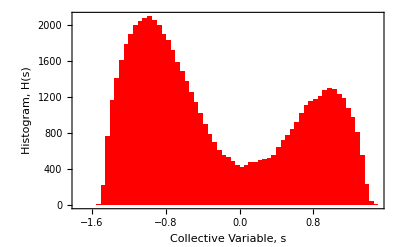

```mathematica
With[{biasedSimulation=Join@@potentialEnergySurfaceEvolution[[All,2]]},
Histogram[biasedSimulation,48,PlotRange->{{-7/4,3/2},Automatic},Frame->True,ChartStyle->Directive[EdgeForm[None], Red],ImageSize->400,LabelStyle->Directive[16,Black],FrameLabel->{"Collective Variable, s","Histogram, H(s)"}]]
```

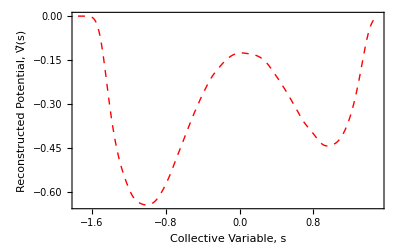

```mathematica
With[{resonstructed=PDF[SmoothKernelDistribution[Join@@potentialEnergySurfaceEvolution[[All,2]],0.05,"Gaussian"]]},
Plot[-resonstructed[s],{s,-7/4,3/2},FrameTicks->{Automatic,None},Frame->True,PlotStyle->Directive[Red,Dashed,Thick],ImageSize->400,LabelStyle->Directive[16,Black],FrameLabel->{"Collective Variable, s","Reconstructed Potential, Ṽ(s)"}]]
```